## ^183Au Fitting the negative parity bands

```mathematica
ClearAll["Global*`"]
```

### Analytical formulae

```mathematica
I0=6.5;
j=6.5;
IF[MOI_]:=1/(2*MOI);
RAD[angle_]:=angle*π/180;
HMin[I_,j_,A1_,A2_,A3_,V_,γ_]:=(A2+A3)(I+j)/2+A1*(I-j)^2-V*(2j-1)/(j+1)*Sin[γ+π/6];
B1[I_,j_,A1_,A2_,A3_,V_,γ_]:=-1*(((2I-1)*(A3-A1)+2j*A1)*((2I-1)*(A2-A1)+2j*A1)+8*A2*A3*I*j+((2j-1)(A3-A1)+2I*A1+V*(2j-1)/(j(j+1))Sqrt[3](Sqrt[3]Cos[γ]+Sin[γ]))*((2j-1)(A2-A1)+2I*A1+V*(2j-1)/(j(j+1))2Sqrt[3]Sin[γ]));
C1[I_,j_,A1_,A2_,A3_,V_,γ_]:=((((2I-1)(A3-A1)+2j*A1)*((2j-1)(A3-A1)+2I*A1+V*(2j-1)/(j(j+1))Sqrt[3](Sqrt[3]Cos[γ]+Sin[γ]))-4I*j*A3^2)*(((2I-1)*(A2-A1)+2j*A1)*((2j-1)(A2-A1)+2I*A1+V*(2j-1)/(j(j+1))2Sqrt[3]Sin[γ])-4I*j*A2^2));
Omega1[I_,j_,A1_,A2_,A3_,V_,γ_]:=Sqrt[1/2(-B1[I,j,A1,A2,A3,V,γ]-Sqrt[B1[I,j,A1,A2,A3,V,γ]^2-4*C1[I,j,A1,A2,A3,V,γ]])];
Omega2[I_,j_,A1_,A2_,A3_,V_,γ_]:=Sqrt[1/2(-B1[I,j,A1,A2,A3,V,γ]+Sqrt[B1[I,j,A1,A2,A3,V,γ]^2-4*C1[I,j,A1,A2,A3,V,γ]])];
Energy[nw1_,nw2_,I_,j_,A1_,A2_,A3_,V_,γ_]:=HMin[I,j,A1,A2,A3,V,γ]+Omega1[I,j,A1,A2,A3,V,γ](nw1+1/2)+Omega2[I,j,A1,A2,A3,V,γ](nw2+1/2);
ExcEn[nw1_,nw2_,I_,A1_,A2_,A3_,V_,γ_]:=Energy[nw1,nw2,I,j,A1,A2,A3,V,γ]-Energy[0,0,I0,j,A1,A2,A3,V,γ];
band1Positive[I_,I1_,I2_,I3_,V_,γ_]:=ExcEn[0,0,I,IF[I1],IF[I2],IF[I3],V,RAD[γ]];
band2Positive[I_,I1_,I2_,I3_,V_,γ_]:=ExcEn[1,0,I,IF[I1],IF[I2],IF[I3],V,RAD[γ]];
```

#### Experimental data

```mathematica
s1Positive=Table[N[i],{i,6.5,32.5,2}];
s2Positive=Table[N[i],{i,11.5,21.5,2}];
yrastPositive=N[{702,867,1151,1530,1983,2492,3049,3655,4308,4986,5677,6375,7103,7848}/1000];
tw1Positive=N[{1739,2178,2684,3243,3840,4464}/1000];
bandHead=yrastPositive[[1]];
yrastPositive=Table[yrastPositive[[i]]-bandHead,{i,1,Length[yrastPositive]}];
tw1Positive=Table[tw1Positive[[i]]-bandHead,{i,1,Length[tw1Positive]}];
```

### Fitting procedure

#### Bounds

```mathematica
i1bounds={75,90};
i2bounds={2,15};
i3bounds={10,35};
vbounds={0.01,5.0};
gmbounds={19.7,25};
```

#### Minimization function

```mathematica
chi2[I1_,I2_,I3_,V_,γ_]:=If[Im[Sqrt[1/(Length[s1Positive]+Length[s2Positive]+1)(Sum[(yrastPositive[[i]]-band1Positive[s1Positive[[i]],I1,I2,I3,V,γ])^2,{i,1,Length[s1Positive]}]+Sum[(tw1Positive[[i]]-band2Positive[s2Positive[[i]],I1,I2,I3,V,γ])^2,{i,1,Length[s2Positive]}])]]==0,Sqrt[1/(Length[s1Positive]+Length[s2Positive]+1)(Sum[(yrastPositive[[i]]-band1Positive[s1Positive[[i]],I1,I2,I3,V,γ])^2,{i,1,Length[s1Positive]}]+Sum[(tw1Positive[[i]]-band2Positive[s2Positive[[i]],I1,I2,I3,V,γ])^2,{i,1,Length[s2Positive]}])],10^7];
min=NMinimize[{chi2[I1,I2,I3,V,γ],i1bounds[[1]]≤I1≤i1bounds[[2]]&&i2bounds[[1]]≤I2≤i2bounds[[2]]&&i3bounds[[1]]≤I3≤i3bounds[[2]]&&vbounds[[1]]≤V≤vbounds[[2]]&&gmbounds[[1]]≤γ≤gmbounds[[2]]},{I1,I2,I3,V,γ}];
params=Values@min[[2]];
rms=min[[1]];
Print["RMS-> ",rms,"\nP -> ",params]
```

RMS-> 0.0735079
P -> {83.458,3.65219,25.586,2.02236,18.5}

## Plot data

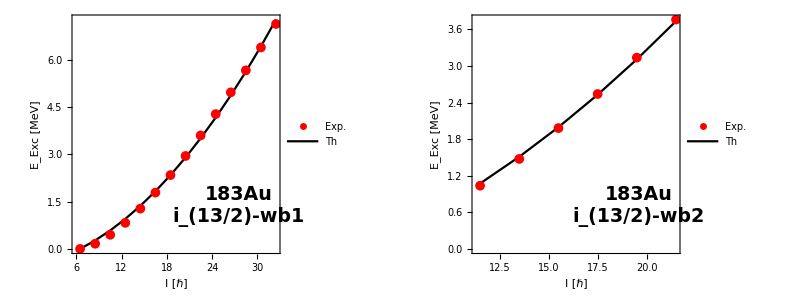

```mathematica
plotFunction[band_,params_,spins_,expData_,label_]:=ListPlot[{Table[{spins[[i]],expData[[i]]},{i,1,Length[spins]}],Table[{spins[[i]],band[spins[[i]],params[[1]],params[[2]],params[[3]],params[[4]],params[[5]]]},{i,1,Length[spins]}]},Frame->True,Axes->False,AspectRatio->0.8,FrameLabel->{"I [ℏ]","E_Exc [MeV]"},PlotLegends->Placed[{"Exp.","Th"},{0.25,0.75}],FrameStyle->Directive[Thick,Black],LabelStyle->{19,Black,Bold,FontFamily->"Times"},Joined->{False, True},PlotStyle->{Red,Black},PlotMarkers->{{Automatic,10},None},Epilog->Inset[Style[label,19,Black,Bold,FontFamily->"Times"],Scaled[{0.8,0.2}]],PlotRange->Full];
plot1=plotFunction[band1Positive,params,s1Positive,yrastPositive,"183Au\ni_(13/2)-wb1"];
plot2=plotFunction[band2Positive,params,s2Positive,tw1Positive,"183Au\ni_(13/2)-wb2"];
Grid[{{Show[plot1,ImageSize->Medium],Show[plot2,ImageSize->Medium]}},Frame->All]
(*Export the plots to files*)
Export["/Users/robertpoenaru/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/183-187Au_Wobbling-Bands/src/python/app/assets/plots/Au_183_plot1Positive.pdf",Show[plot1],ImageResolution->1200];
Export["/Users/robertpoenaru/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/183-187Au_Wobbling-Bands/src/python/app/assets/plots/Au_183_plot2Positive.pdf",Show[plot2],ImageResolution->1200];
```

## Printer function

```mathematica
printer[params_,spins_,expdata_,modelband_]:=Do[Print[spins[[i]]," ",expdata[[i]]," ",modelband[spins[[i]],params[[1]],params[[2]],params[[3]],params[[4]],params[[5]]]],{i,1,Length[spins]}];tabular[params_,spins_,expdata_,modelband_]:=Table[{spins[[i]],expdata[[i]],modelband[spins[[i]],params[[1]],params[[2]],params[[3]],params[[4]],params[[5]]]},{i,1,Length[spins]}];
grider[title_,rms_,params_,spins_,expdata_,modelband_]:=Grid[{{title},{StringTemplate["RMS = ``"][rms]},{StringTemplate["P=I1=`` I2=`` I3=``\nV=`` gm=``"][params[[1]],params[[2]],params[[3]],params[[4]],params[[5]]]},{Grid[tabular[params,spins,expdata,modelband]]}},ItemStyle->{14,Black},FrameStyle->Directive[Black,Thick],Frame->All,Background->{None,{Green}}];
```

```mathematica
pp=params;
grider["Band-1 ; j=i_(13/2)",chi2[pp[[1]],pp[[2]],pp[[3]],pp[[4]],pp[[5]]],pp,s1Positive,yrastPositive,band1Positive]
grider["Band-2 ; j=i_(13/2)",chi2[pp[[1]],pp[[2]],pp[[3]],pp[[4]],pp[[5]]],pp,s2Positive,tw1Positive,band2Positive]
```

Band-1 ; j=i_(13/2)
RMS = 0.0735079
P=I1=83.458 I2=3.65219 I3=25.586
V=2.02236 gm=18.5
6.5 | 0. | 0.
8.5 | 0.165 | 0.268971
10.5 | 0.449 | 0.586885
12.5 | 0.828 | 0.953662
14.5 | 1.281 | 1.36918
16.5 | 1.79 | 1.83331
18.5 | 2.347 | 2.34594
20.5 | 2.953 | 2.907
22.5 | 3.606 | 3.5164
24.5 | 4.284 | 4.17409
26.5 | 4.975 | 4.88
28.5 | 5.673 | 5.63411
30.5 | 6.401 | 6.43636
32.5 | 7.146 | 7.28674

Band-2 ; j=i_(13/2)
RMS = 0.0735079
P=I1=83.458 I2=3.65219 I3=25.586
V=2.02236 gm=18.5
11.5 | 1.037 | 1.07302
13.5 | 1.476 | 1.51164
15.5 | 1.982 | 1.99726
17.5 | 2.541 | 2.5299
19.5 | 3.138 | 3.10959
21.5 | 3.762 | 3.73636